## Union 2 supernova (http://supernova.lbl.gov/Union/) Data file from: http://supernova.lbl.gov/Union/figures/SCPUnion2.1_mu _vs _z.txt

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
c=3.00*10^8 m s^-1;

yr=365.25*(24*3600)s;

km=10^3 m;

pc=3.26*c*yr;

Mpc=10^6pc;

Gyr=10^9yr;
```

```mathematica
H0[h_]=100.km s^-1 Mpc^(-1)h
```

(3.24009×10^-18 h)/s

Load data from file

```mathematica
LD[μ_]:=10^(0.2 μ+1)

LDe[μ_,δμ_]:=0.461 LD[μ]δμ (*error on luminosity dist from dist mod and its error*)
```

```mathematica
Print["\n\nFormat:  sn id,  Z,  dist mod μ,  err in μ\n\n"];

sndata=Import[StringJoin[NotebookDirectory[],"SCPUnion2.1_mu_vs_z.txt"],"Table"][[6;;-1]];

size=Length[sndata];

getZ[ii_]:=sndata[[ii,2]];

getμ[ii_]:=sndata[[ii,3]];

getμerr[ii_]:=sndata[[ii,4]];

getLd[ii_]:=LD[sndata[[ii,3]]];

getLderr[ii_]:=LDe[sndata[[ii,3]],sndata[[ii,4]]];
```

Format:  sn id,  Z,  dist mod μ,  err in μ

```mathematica
dataweights;
```

```mathematica
datafit=Table[{getZ[ii],getLd[ii]},{ii,1,size}];

dataweights=Table[1/getLderr[ii]^2,{ii,1,size}];
```

```mathematica
error=Table[getLderr[ii],{ii,1,size}];
```

Plots from data

μ vs Z

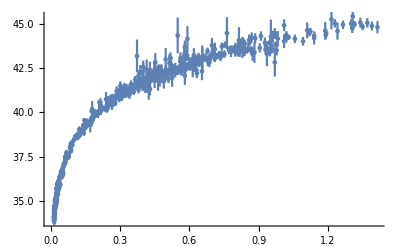

```mathematica
Print["\n\nμ vs Z\n"]

ErrorListPlot[Table[{getZ[ii],getμ[ii],getμerr[ii]},{ii,1,size}]]
```

```mathematica
getLderr
```

getLderr

Ld (/pc) vs Z

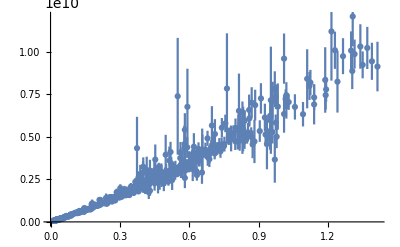

```mathematica
Print["\n\nLd (/pc) vs Z\n"]
dataplt=ErrorListPlot[Table[{getZ[ii],getLd[ii],getLderr[ii]},{ii,1,size}]]
```

Estimate cosmological parameters: Flat universe

```mathematica
dL[z_,h_,ΩM_]=c(1+z)/H0[h]*FullSimplify[Integrate[1/(x^2Sqrt[(1-ΩM)+ΩM/x^3]),{x,1/(1+z),1}],{1>ΩM>0,z>0}];
```

ConditionalExpression[(9.259×10^25 m (1+z) (-Hypergeometric2F1[1/3,1/2,4/3,ΩM/(-1+ΩM)]+(1+z) Hypergeometric2F1[1/3,1/2,4/3,((1+z)^3 ΩM)/(-1+ΩM)]))/(h √(1-ΩM)),(Re[(-(-1+ΩM)^(1/3)+(-1)^(2/3) (1+z) ΩM^(1/3))/(-1+ΩM)^(1/3)]≥z||Re[(-(-1+ΩM)^(1/3)+(-1)^(2/3) (1+z) ΩM^(1/3))/(-1+ΩM)^(1/3)]≤0||(-(-1+ΩM)^(1/3)+(-1)^(2/3) (1+z) ΩM^(1/3))/(-1+ΩM)^(1/3)∉Reals)&&(Re[(-(-1+ΩM)^(1/3)-(1+z) (-ΩM)^(1/3))/(-1+ΩM)^(1/3)]≥z||Re[(-(-1+ΩM)^(1/3)-(1+z) (-ΩM)^(1/3))/(-1+ΩM)^(1/3)]≤0||(-(-1+ΩM)^(1/3)-(1+z) (-ΩM)^(1/3))/(-1+ΩM)^(1/3)∉Reals)&&(Re[(-(-1+ΩM)^(1/3)+(1+z) ΩM^(1/3))/(-1+ΩM)^(1/3)]≥z||Re[(-(-1+ΩM)^(1/3)+(1+z) ΩM^(1/3))/(-1+ΩM)^(1/3)]≤0||(-(-1+ΩM)^(1/3)+(1+z) ΩM^(1/3))/(-1+ΩM)^(1/3)∉Reals)]

```mathematica
datafit=Table[{getZ[ii],getLd[ii]},{ii,1,size}];

dataweights=Table[1/getLderr[ii]^2,{ii,1,size}];
```

```mathematica
fit=NonlinearModelFit[datafit,1/pc*dL[z,h,ΩM],{{h,0.7},{ΩM,0.3}},z,Weights->dataweights];
```

```mathematica
param=fit["BestFitParameters"];

Print["\n\nBest fit parameters = ",param];

Print["\n\n95% confidence:     = ",fit["ParameterConfidenceIntervals",ConfidenceLevel->.95],"\n\n"];

Print["\n\n   h  = ",h/.param," +- ",fit["ParameterConfidenceIntervals",ConfidenceLevel->.95][[1,2]]-h/.param];

Print["\n\n   ΩM = ",ΩM/.param," +- ",fit["ParameterConfidenceIntervals",ConfidenceLevel->.95][[2,2]]-ΩM/.param,"\n\n"];

fitplt=Plot[fit[z],{z,0,1.5},PlotStyle->{Hue[0],Thickness[0.007]}];

Print["\n\nAge of universe (/Gyr) = ",1/Gyr Age[h,ΩM]/.param,"\n\nΩΛ = ",1-ΩM/.param,"\n\n"];
```

Best fit parameters = {h→0.704314,ΩM→0.296869}

95% confidence:     = {{0.697731,0.710896},{0.258587,0.335152}}

h  = 0.704314 +- 0.00658272

ΩM = 0.296869 +- 0.0382825

Age of universe (/Gyr) = (3.16881×10^-17 Age[0.704314,0.296869])/s

ΩΛ = 0.703131

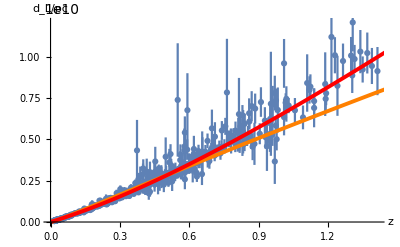

```mathematica
Show[dataplt,Plot[(4.66228*10^9 (-1+(1+z)^(3/2))^1.15654)/(1+z)^0.734812,{z,0,1.5},PlotStyle->{Orange, Thickness[0.007]}],Plot[5.20394*10^9 (1+z) (-0.950119+(1+z) Hypergeometric2F1[1/3,1/2,4/3,-0.475466 (1+z)^3]),{z,0,1.5},PlotStyle->{Red, Thickness[0.007]}],AxesLabel->{"z","d_L/pc"}]
```

Estimate cosmological parameters: fractal universe

```mathematica
b=(9/2)^(1/3)*(4.3)^((2+d)/3) σ*((1+z)^(3/2)-1)^(d/3)/(1+z)^(d/2-1)
```

(3^(2/3) 4.3^((2+d)/3) (1+z)^(1-d/2) (-1+(1+z)^(3/2))^(d/3) σ)/2^(1/3)

```mathematica
dLf[z_,σ_,d_]=FullSimplify[10^9 b,{σ>0,d>0,z>0}]
```

4.36566×10^9 ⅇ^(0.486205 d) (1+z)^(-d/2) (1.+z) (-1+(1+z)^(3/2))^(d/3) σ

```mathematica
datafitf=Table[{getZ[ii],getLd[ii]},{ii,1,size}];

dataweightsf=Table[1/getLderr[ii]^2,{ii,1,size}];
```

```mathematica
fitf=NonlinearModelFit[datafitf,dLf[z,σ,d],{{σ,1},{d,3}},z,Weights->dataweights];
```

```mathematica
paramf=fitf["BestFitParameters"];

Print["\n\nBest fit parameters = ",paramf];

Print["\n\n95% confidence:     = ",fitf["ParameterConfidenceIntervals",ConfidenceLevel->.95],"\n\n"];

Print["\n\n   σ  = ",σ/.paramf," +- ",fitf["ParameterConfidenceIntervals",ConfidenceLevel->.95][[1,2]]-σ/.paramf];

Print["\n\n   d = ",d/.paramf," +- ",fitf["ParameterConfidenceIntervals",ConfidenceLevel->.95][[2,2]]-d/.paramf,"\n\n"];

fitpltf=Plot[fitf[z],{z,0,1.5},PlotStyle->{Orange,Thickness[0.007]}];
```

Best fit parameters = {σ→0.191939,d→3.43755}

95% confidence:     = {{0.190221,0.193658},{3.41006,3.46504}}

σ  = 0.191939 +- 0.00171812

d = 3.43755 +- 0.0274906

```mathematica
datafitf=Table[{getZ[ii],getLd[ii]},{ii,1,size}];

dataweightsf=Table[1/getLderr[ii]^2,{ii,1,size}];
frac=(10^9*(9/2)^(1/3)*(4.3)^((2+d)/3) σ*((1+z)^(3/2)-1)^(d/3)/(1+z)^(d/2-1))
hello=+(HeavisideTheta[z-q])*frac/.σ->μ/.d->3;
coucou=(HeavisideTheta[z+0.1]-HeavisideTheta[z-q])*frac;
newmodel=hello+coucou
fitg=NonlinearModelFit[datafitf,newmodel,{{σ,1},{d,3},{μ,1},{q,0.63}},z,Weights->dataweights];
paramg=fitg["BestFitParameters"];

Print["\n\nBest fit parameters = ",paramg];

Print["\n\n95% confidence:     = ",fitg["ParameterConfidenceIntervals",ConfidenceLevel->.95],"\n\n"];

Print["\n\n   σ  = ",σ/.paramg," +- ",fitg["ParameterConfidenceIntervals",ConfidenceLevel->.95][[1,2]]-σ/.paramg];

Print["\n\n   d = ",d/.paramg," +- ",fitg["ParameterConfidenceIntervals",ConfidenceLevel->.95][[2,2]]-d/.paramg,"\n\n"];

fitpltg=Plot[fitg[z],{z,0,1.5},PlotStyle->{Green,Thickness[0.007]}];
```

500000000 4.3^((2+d)/3) 6^(2/3) (1+z)^(1-d/2) (-1+(1+z)^(3/2))^(d/3) σ

500000000 4.3^((2+d)/3) 6^(2/3) (1+z)^(1-d/2) (-1+(1+z)^(3/2))^(d/3) σ (HeavisideTheta[0.1+z]-HeavisideTheta[-q+z])+(1.87723×10^10 (-1+(1+z)^(3/2)) μ HeavisideTheta[-q+z])/(√(1+z))

Best fit parameters = {σ→0.187503,d→3.36509,μ→0.254975,q→0.63}

95% confidence:     = {{0.185836,0.18917},{3.33857,3.3916},{0.248934,0.261017},{0.63,0.63}}

σ  = 0.187503 +- 0.00166692

d = 3.36509 +- 0.0265168

### Final plot :

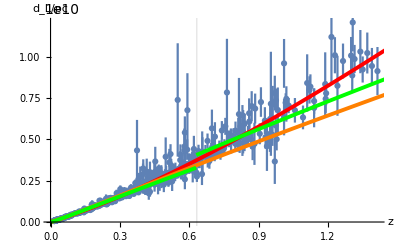

```mathematica
Show[dataplt,fitplt,fitpltf,fitpltg,AxesLabel->{"z","d_L/pc"},GridLines->{{0.633},None}]
```

#### Decide which Fit is the best:

```mathematica
residf=fitf["FitResiduals"];
```

```mathematica
resid=fit["FitResiduals"];
```

diviser les residus par les données

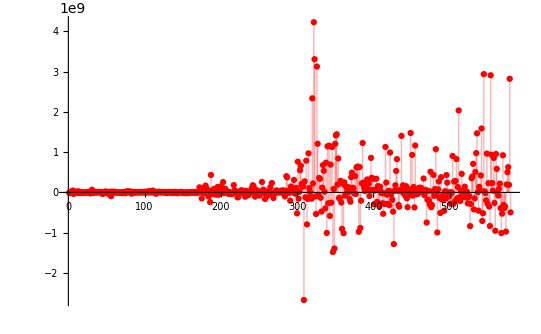

```mathematica
ListPlot[{resid},Filling->Axis,PlotStyle->Red,PlotRange->Full]
```

```mathematica
Show[%86,PlotLabel->None,LabelStyle->{11,GrayLevel[.5]}];
```

```mathematica
Show[%53,Axes->False];
```

Show::gcomb: Could not combine the graphics objects in Show[{{0.028488, 1.17305×10^8}, {0.050043, 2.17007×10^8}, {0.052926, 2.30961×10^8}, {0.070086, 3.08565×10^8}, {0.062668, 3.13821×10^8}, {0.087589, 4.42396×10^8}, {0.078577, 3.14509×10^8}, {0.017227, 8.52853×10^7}, {0.042233, 1.85051×10^8}, {0.045295, 2.12841×10^8}, « 31 », {0.031528, 1.39879×10^8}, {0.023536, 1.08123×10^8}, {0.016743, 6.3175×10^7}, {0.05371, 1.97373×10^8}, {0.016991, 7.51198×10^7}, {0.027865, 1.04394×10^8}, {0.017173, 7.11433×10^7}, {0.029955, 1.56477×10^8}, {0.016559, 7.39208×10^7}, « 530 »}, Axes → False].

```mathematica
Show[%77,Axes->{True,False},Ticks->{None,Automatic}];
```

Show::gtype: Real is not a type of graphics.

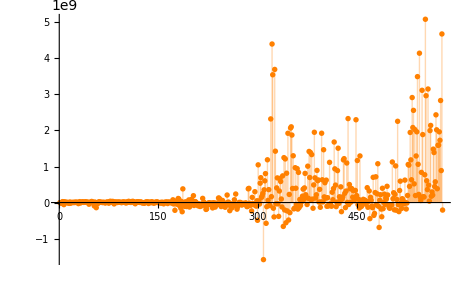

```mathematica
ListPlot[{residf},Filling->Axis,PlotStyle-> Orange,PlotRange->Full,LabelStyle->{11,GrayLevel[.5]}]
```

```mathematica
bien=fit["RSquared"]
bene=fit["AdjustedRSquared"]
```

0.994108

0.994088

```mathematica
bienf=fitf["RSquared"]
benef=fitf["AdjustedRSquared"]
```

0.989355

0.989318

```mathematica
contour3=fit["ParameterConfidenceRegion",ConfidenceLevel-> 0.95]
contour5=fit["ParameterConfidenceRegion",ConfidenceLevel-> 0.99]
contourf=fitf["ParameterConfidenceRegion"]
```

FittedModels`ParameterEllipsoid[{0.704314,0.296869},{0.0482244,0.00548986},{{-0.127837,0.991795},{-0.991795,-0.127837}}]

FittedModels`ParameterEllipsoid[{0.704314,0.296869},{0.0598748,0.00681615},{{-0.127837,0.991795},{-0.991795,-0.127837}}]

FittedModels`ParameterEllipsoid[{0.191939,3.43755},{0.0343564,0.00203192},{{0.0202006,0.999796},{-0.999796,0.0202006}}]

```mathematica
Point[h,ΩM]/.fit["BestFitParameters"]
```

Point[0.704314,0.296869]

```mathematica
ells=Table[fit["ParameterConfidenceRegion",ConfidenceLevel->c],{c,{.68,.95,0.99}}]
ellsf=Table[fitf["ParameterConfidenceRegion",ConfidenceLevel->c],{c,{0.68,.95,0.99}}];
```

{FittedModels`ParameterEllipsoid[{0.704314,0.296869},{0.0296935,0.00338031},{{-0.127837,0.991795},{-0.991795,-0.127837}}],FittedModels`ParameterEllipsoid[{0.704314,0.296869},{0.0482244,0.00548986},{{-0.127837,0.991795},{-0.991795,-0.127837}}],FittedModels`ParameterEllipsoid[{0.704314,0.296869},{0.0598748,0.00681615},{{-0.127837,0.991795},{-0.991795,-0.127837}}]}

```mathematica
Graphics[{Thickness[0.001],ells}, Frame->True, FrameTicks->{{{0.25,0.27,0.29,0.31,0.33,0.35},None},{{0.70,0.71},None}},FrameLabel->{"h","Ω_M"} ]
```

-Graphics-

```mathematica
Graphics[{{Directive[AbsolutePointSize[4],Red],Point[{h,ΩM}/.fit["BestFitParameters"]]},Thickness[0.01],MapThread[Tooltip[{#1,#2},StringForm["α = `1`",InputForm[#3]]]&,{ColorData[1]/@Range[3],ells,{.68,.95,.99}}]}, Frame->True, FrameTicks->{{{0.25,0.27,0.29,0.31,0.33,0.35},None},{{0.70,0.71},None}},FrameLabel->{"h","Ω_M"} ]
```

-Graphics-

```mathematica
Graphics[{Thickness[0.01],ellsf}, Frame->True,FrameTicks->{{{3.41,3.42,3.43,3.44,3.45,3.46},None},{{0.192},None}},FrameLabel->{"σ","d"}]
```

-Graphics-

```mathematica
Graphics[{{Directive[AbsolutePointSize[4],Red],Point[{σ,d}/.fitf["BestFitParameters"]]},MapThread[Tooltip[{#1,#2},StringForm["α = `1`",InputForm[#3]]]&,{ColorData[1]/@Range[3],ellsf,{0.68,.95,.99}}]},Frame->True,FrameTicks->{{{3.41,3.42,3.43,3.44,3.45,3.46},None},{{0.192},None}},FrameLabel->{"σ","d"}]
```

-Graphics-